## Common

```mathematica
Needs["PlotLegends`"]
```

```mathematica
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
```

```mathematica
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
```

This function reads single stat for all experiment runs by multiple parameters/methods. Typical use for "experiments_???.txt" file.

```mathematica
readFinalStats[names_List,statName_]:=
Module[{allData},
allData = ImportString[Import[#],"TSV"]&/@names;
allData⟦#⟦1⟧,2;;,#⟦3⟧⟧&/@Position[allData,statName]
]
```

Reads all stat names from multiple parameters/methods. Returns their intersection.

```mathematica
readFinalStatNames[names_List]:=
Module[{allData},
Flatten[Intersection[(ImportString[Import[#],"TSV"]&/@names)⟦All,1,All⟧]]
]
```

```mathematica
listAllExperimentFiles[dirs_List]:=
Flatten[FileNames[RegularExpression["experiments\\_\\d\\d\\d\\.txt"],{"/Users/drchaj1/java/exp/"<>#}]&/@dirs]
```

## Fitness of a Single Run

```mathematica
{data, bsf, avg, med, min}=readRunFitness["~/java/exp/results/run_001_001_FITNESS.txt"];
```

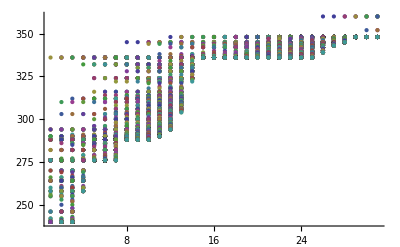

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

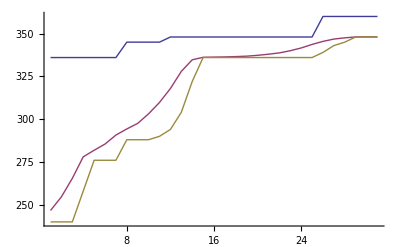

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

## Fitness over Multiple Runs

```mathematica
bsfAvg = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

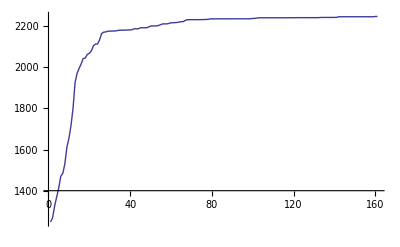

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

## Evaluation of a Single Run

```mathematica
{data, max, avg, med, min}=readRunEvaluationInfo["~/java/exp/results/run_001_001_AVG_DISTANCE.txt"];
```

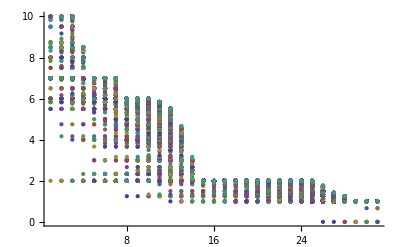

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

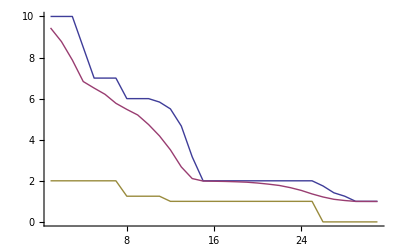

```mathematica
ListLinePlot[{max, avg, min}, PlotRange->All]
```

## Evaluation over Multiple Runs

```mathematica
bsfAvg = (readRunEvaluationInfo[#]⟦5⟧&/@FileNames["run_001*AVG_DISTANCE.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
bsfAvg=Mean[enlarge[#,Min[bsfAvg], bsfAvg]&/@bsfAvg];
```

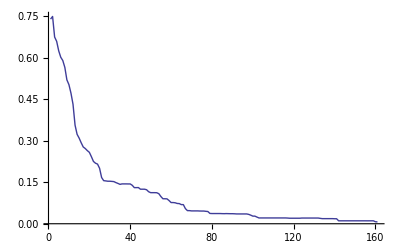

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

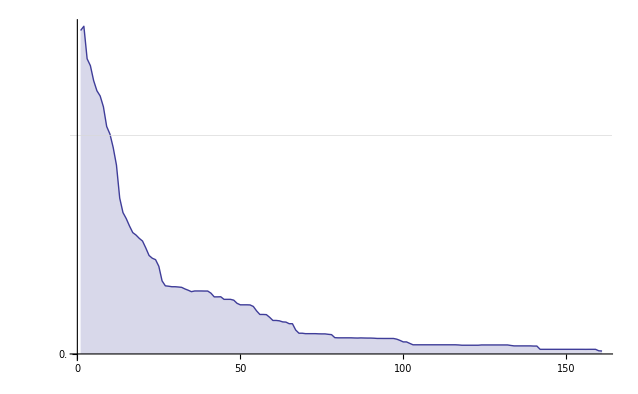

```mathematica
Show[ListLinePlot[{bsfAvg[[1;;]]}, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},Filling->Axis,AxesOrigin->{0,0}], GridLines->{None, {0.5}}]
```

## Evaluation over Multiple Methods

```mathematica
singleMethod[methodDir_, variable_, column_] :=
Module[{stat},
stat=(readRunFitness[#]⟦column⟧&/@(Complement[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]));
Mean[enlarge[#,Max[#], stat]&/@stat]
]
```

```mathematica
singleMethodGeneralization[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
Intersection[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]);
Mean[enlarge[#,Min[#], stat]&/@stat]
]
```

```mathematica
singleMethodDiversity[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
FileNames["run_001_*"<>variable<>"*.txt",{"~/java/exp/results/"<>methodDir}]);
Rescale[Mean[enlarge[#,Mean[#], stat]&/@stat]];
Mean[enlarge[#,Mean[#], stat]&/@stat]
]
```

```mathematica
multipleMethods[methodDirs_, variable_, column_, generalization_:True] :=
Module[{stats, len},
If[generalization==True,
stats=(singleMethod[#,variable, column]&/@methodDirs)~Join~(singleMethodGeneralization[#,variable]&/@methodDirs),
stats=(singleMethod[#,variable, column]&/@methodDirs)];
len = Max[Length/@stats];
stats=enlarge[#,Min[#], stats, len]&/@stats;
Show[
ListLinePlot[stats, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},AxesOrigin->{0,0}, PlotStyle->{Thickness[0.005]},
PlotLegend->methodDirs~Join~(StringJoin[#," G"]&/@methodDirs),
PlotMarkers->Automatic,
LegendPosition->{1.1,-0.4}
], 
GridLines->{None, {0.5}}]
]
```

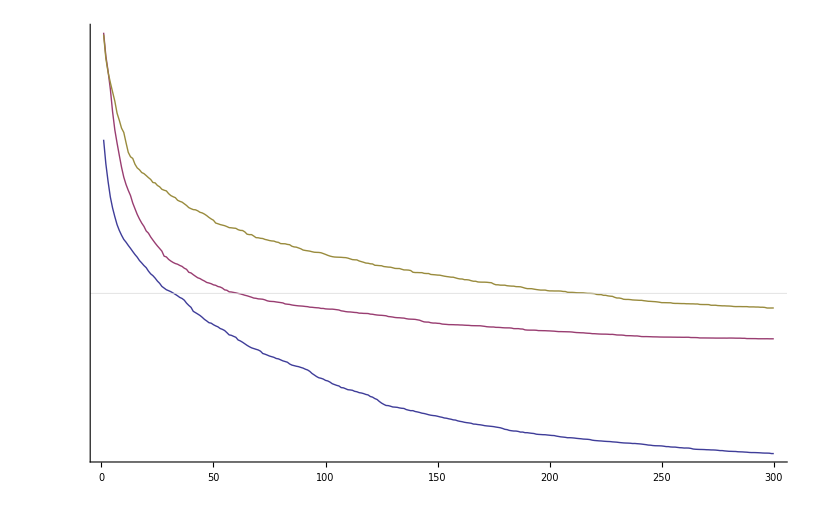

```mathematica
multipleMethods[{"FC_NEAT", "FC_GP", "FC_GPDC"}, "AVG_DISTANCE", 5]
```

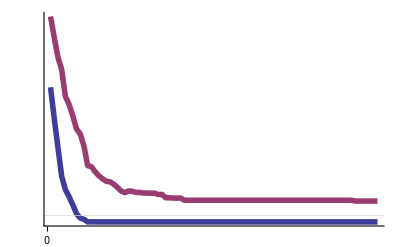

```mathematica
multipleMethods[{"T_NEAT", "T_GP"}, "AVG_DISTANCE", 5]
```

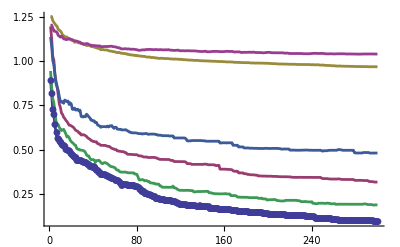

```mathematica
multipleMethods[{"FC_NEAT_7_20", "FC_GP_7_20", "FC_SADE_7_20"}, "AVG_DISTANCE", 5]
```

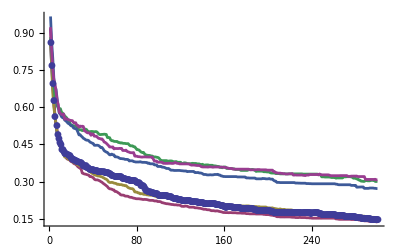

```mathematica
multipleMethods[{"DIV_GP_5_50", "DIV_NEAT_5_50", "DIV_NEAT_5_50_AMP10"}, "AVG_DISTANCE", 5]
```

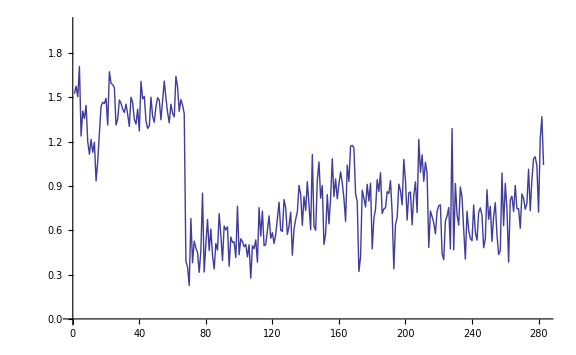

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

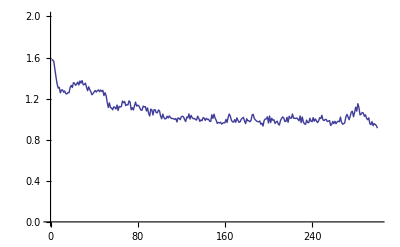

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

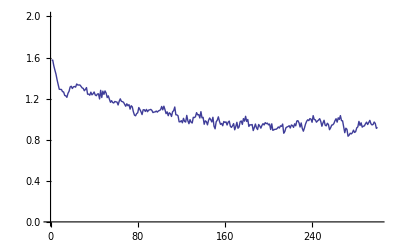

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50_AMP10"},"DIVERSITY"],PlotRange->{0,2}]
```

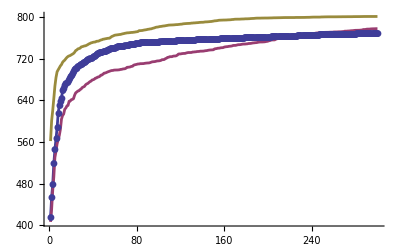

```mathematica
multipleMethods[{"DIV_GP_7_50","DIV_GPC_7_50", "DIV_NEAT_7_50"}, "FITNESS", 2, False]
```

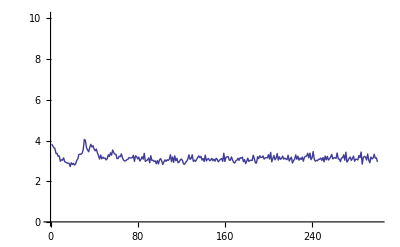

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

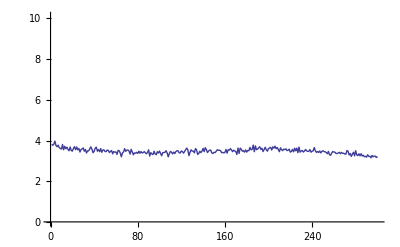

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

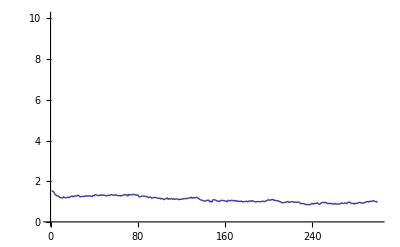

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

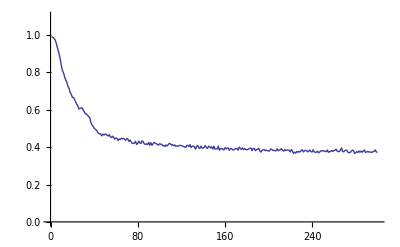

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

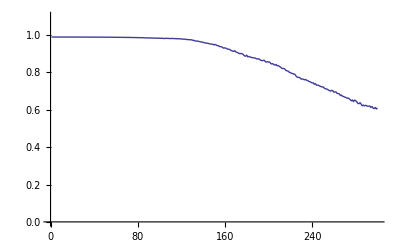

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

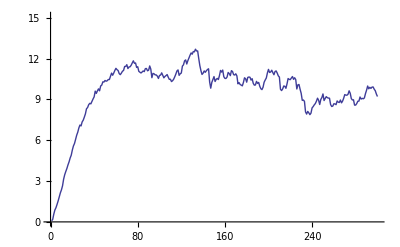

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"G_DIVERSITY"],PlotRange->{0,15.1}]
```

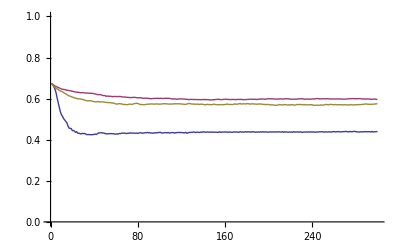

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_ROULETTE"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_TOURNAMENT2"},"G_DIVERSITY"]},PlotRange->{0,1}]
```

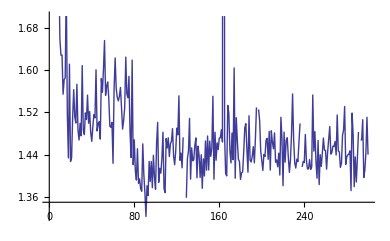

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"P_DIVERSITY"]}]
```

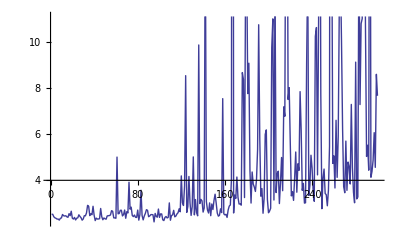

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT2"},"P_DIVERSITY"]}]
```

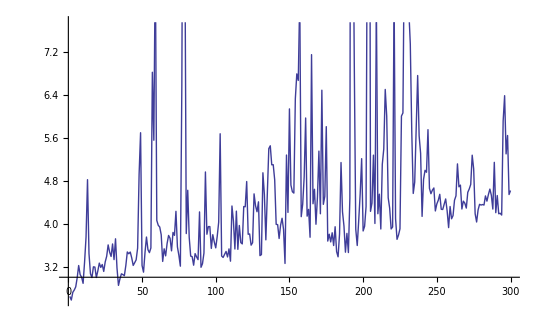

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_ROULETTE"},"P_DIVERSITY"]}]
```

## Final Stats

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","O_","C_"},{"A","B","C","D","E","F","G","H","I","FC","K"}]]
```

{GP_A,GP_B,GP_C,GP_D,GP_E,GP_F,GP_G,GP_H,GP_I,GP_FC,GP_K,O_A,O_B,O_C,O_D,O_E,O_F,O_G,O_H,O_I,O_FC,O_K,C_A,C_B,C_C,C_D,C_E,C_F,C_G,C_H,C_I,C_FC,C_K}

```mathematica
files= listAllExperimentFiles[{"20110717/GP4D","20110717/GPAT4D","GPAT4D_EC"}]
```

{/Users/drchaj1/java/exp/20110717/GP4D/experiments_001.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_002.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_003.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_004.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_005.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_006.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_007.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_008.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_009.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_010.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_001.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_002.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_003.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_004.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_005.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_006.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_007.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_008.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_009.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_010.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_001.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_002.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_003.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_004.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_005.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_006.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_007.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_008.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_009.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_010.txt}

```mathematica
labels=Flatten[Transpose[Partition[labels,Length[labels]/3]]]
```

{GP_A,O_A,C_A,GP_B,O_B,C_B,GP_C,O_C,C_C,GP_D,O_D,C_D,GP_E,O_E,C_E,GP_F,O_F,C_F,GP_G,O_G,C_G,GP_H,O_H,C_H,GP_I,O_I,C_I,GP_FC,O_FC,C_FC,GP_K,O_K,C_K}

```mathematica
files=Flatten[Transpose[Partition[files,Length[files]/3]]]
```

{/Users/drchaj1/java/exp/20110717/GP4D/experiments_001.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_001.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_001.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_002.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_002.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_002.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_003.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_003.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_003.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_004.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_004.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_004.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_005.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_005.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_005.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_006.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_006.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_006.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_007.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_007.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_007.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_008.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_008.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_008.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_009.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_009.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_009.txt,/Users/drchaj1/java/exp/20110717/GP4D/experiments_010.txt,/Users/drchaj1/java/exp/20110717/GPAT4D/experiments_010.txt,/Users/drchaj1/java/exp/GPAT4D_EC/experiments_010.txt}

```mathematica
files=listAllExperimentFiles[labels]
```

{/Users/drchaj1/java/exp/GP_I/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_I/experiments_001.txt,/Users/drchaj1/java/exp/GP_J/experiments_001.txt,/Users/drchaj1/java/exp/GP_K/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_K/experiments_001.txt}

```mathematica
readFinalStatNames[files]
```

{BSF,BSFG,ARITY_BSF,ARITY_LG,CONSTANTS_BSF,CONSTANTS_LG,DEPTH_BSF,DEPTH_LG,LEAVES_BSF,LEAVES_LG,NODES_BSF,NODES_LG,GENERATIONS,EVALUATIONS,MAX_FITNESS,SUCCESS,TIME}

```mathematica
Clear[finalStatsAll];
```

```mathematica
finalStatsAll[files_,methods_,sortBy_:Null,colors_:"Rainbow"]:=
Module[{statNames,statPosition,data,order,labels,success},
(* Names of all stats. *)
statNames=readFinalStatNames[files];
(* A position of a stat to sort by. *)
statPosition=Flatten[Position[statNames,sortBy]];
data=readFinalStats[files,#]&/@statNames;
(* No sort-by stat given or not existing one given. *)
If[Length[statPosition]==1,
order=Ordering[Median/@data[[statPosition⟦1⟧]]],
order=Range[Length[files]]
];
(* Sort data and labels. *)
data=Part[#,order]&/@data;
labels =methods⟦order⟧;

(* Compute % of sucessful runs *) 
success=100*Count[#,"true"]/Length[#]&/@data⟦Sequence@@Flatten[Position[statNames,"SUCCESS"]]⟧;

(* Print them as a table. *)
Print[Grid[Transpose@{{Style["ID",Bold]}~Join~labels,{Style["SUCCESS %",Bold]}~Join~success},Frame->All]];
(* And a bar chart. *)
Print[BarChart[success,ChartLabels->labels,ChartStyle->colors,LabelingFunction->Center,ImageSize->1200]];
(* All other stats as box plots.*)
Grid[Transpose[{statNames,
BoxWhiskerChart[#,"Notched",ChartLabels->(labels),ChartStyle->colors,ImageSize->800]&
/@data
}]]
]
```

ID | SUCCESS %
GP_A | 97
O_A | 100
C_A | 98
GP_B | 78
O_B | 98
C_B | 99
GP_C | 91
O_C | 98
C_C | 95
GP_D | 25
O_D | 0
C_D | 1
GP_E | 43
O_E | 0
C_E | 0
GP_F | 33
O_F | 6
C_F | 9
GP_G | 25
O_G | 19
C_G | 26
GP_H | 23
O_H | 3
C_H | 11
GP_I | 12
O_I | 0
C_I | 1
GP_FC | 75
O_FC | 0
C_FC | 0

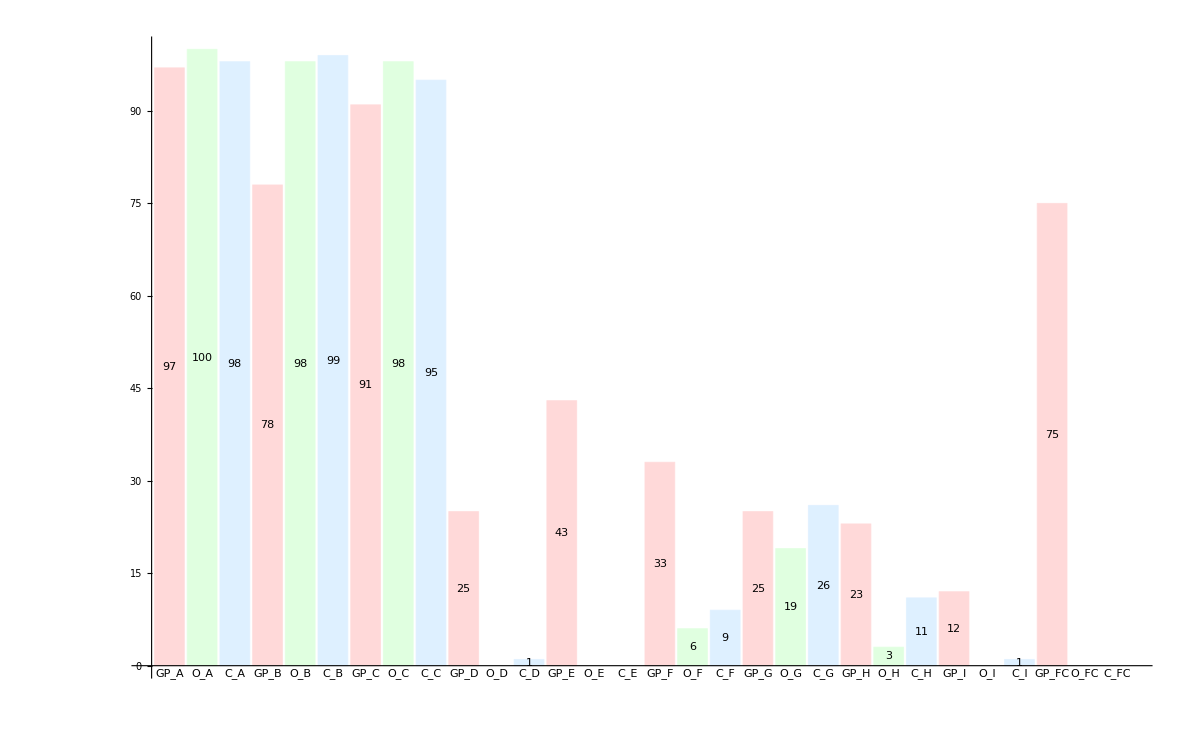

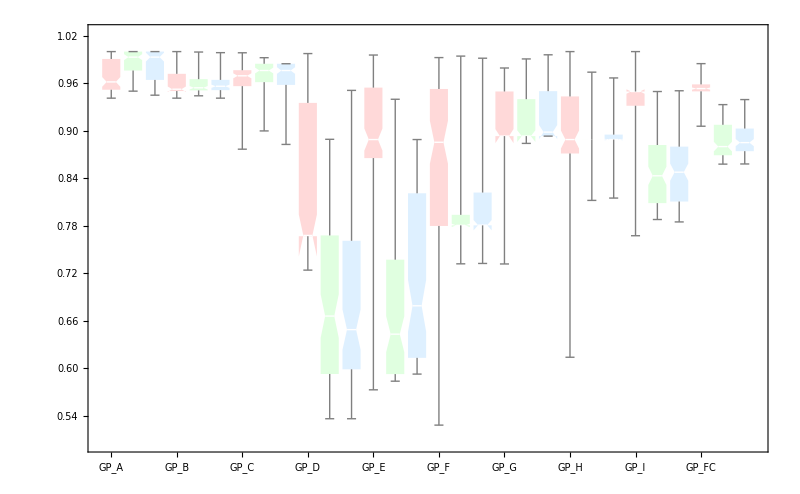
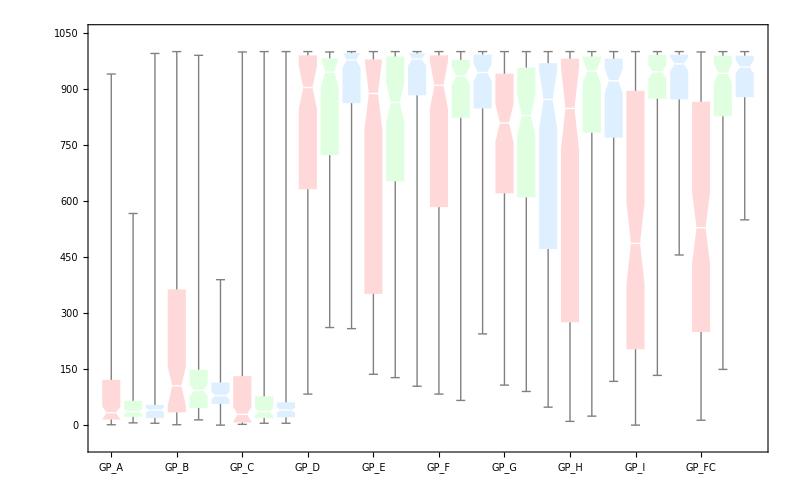
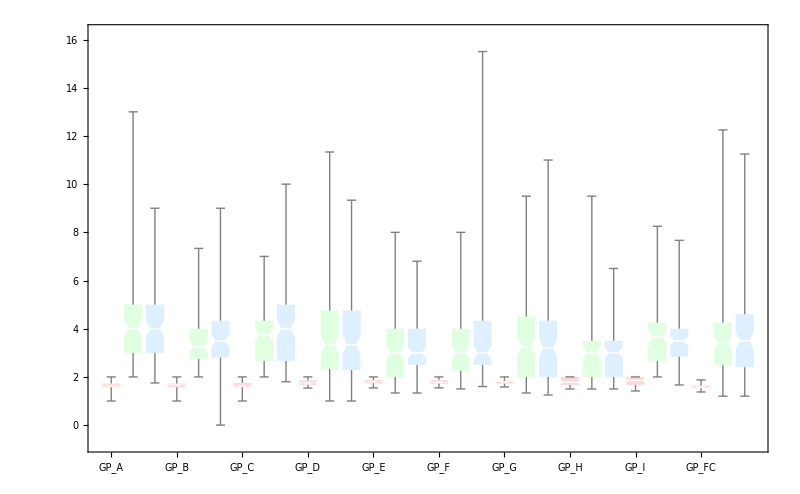
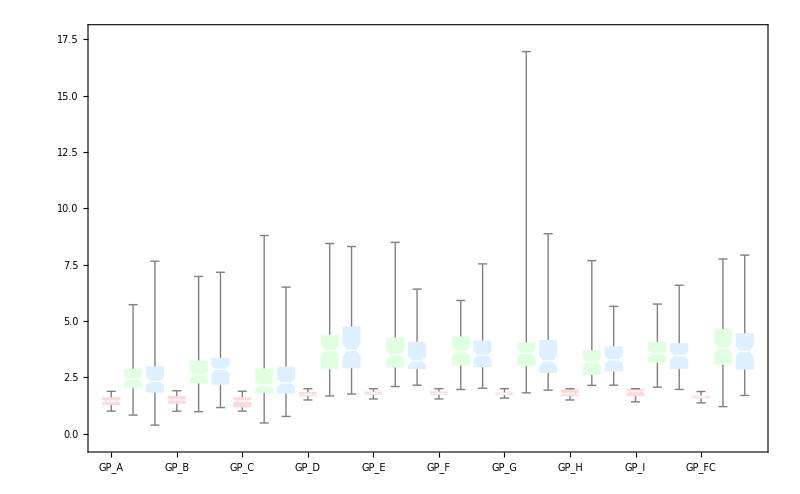
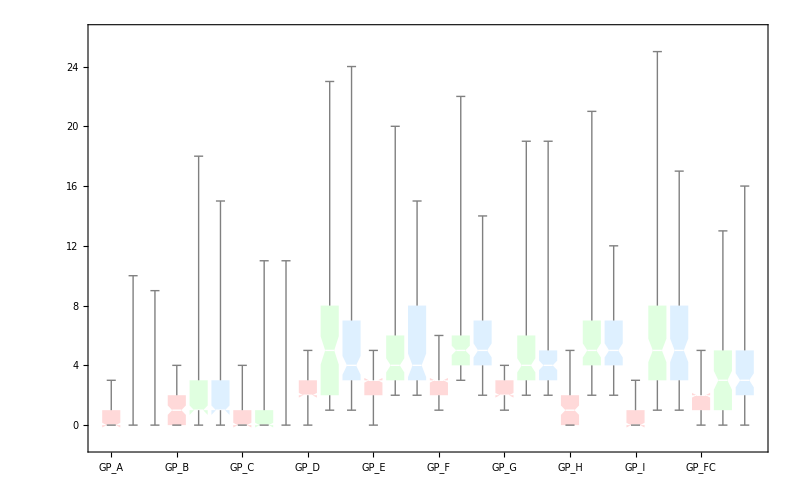
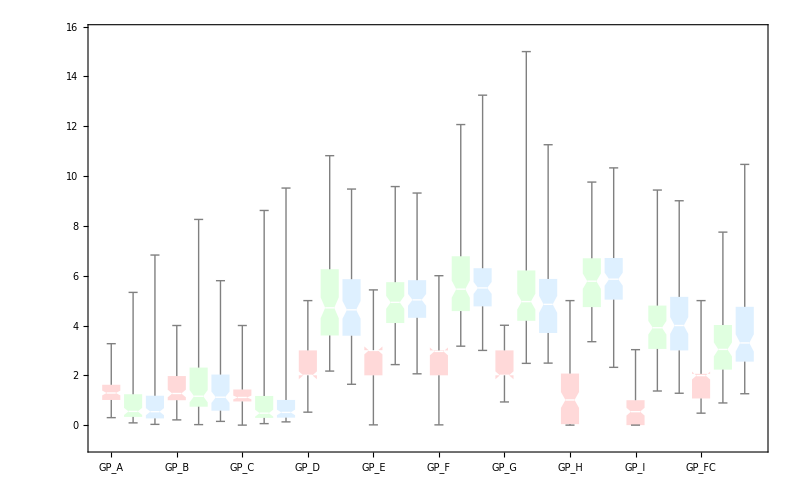
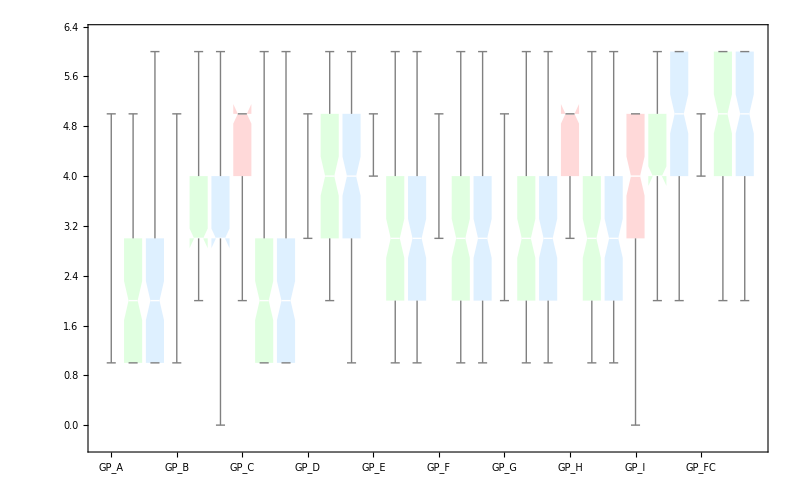
BSF | -Graphics-
BSFG | -Graphics-
ARITY_BSF | -Graphics-
ARITY_LG | -Graphics-
CONSTANTS_BSF | -Graphics-
CONSTANTS_LG | -Graphics-
DEPTH_BSF | -Graphics-
DEPTH_LG | -Graphics-
LEAVES_BSF | -Graphics-
LEAVES_LG | -Graphics-
NODES_BSF | -Graphics-
NODES_LG | -Graphics-
GENERATIONS | -Graphics-
EVALUATIONS | -Graphics-
MAX_FITNESS | -Graphics-
SUCCESS | -Graphics-
TIME | -Graphics-

```mathematica
finalStatsAll[files,labels,Null,{LightRed,LightGreen,LightBlue}]
```